## how neural networks work

```mathematica
RandomVariate[NormalDistribution[.1,.5]]
```

-0.196999

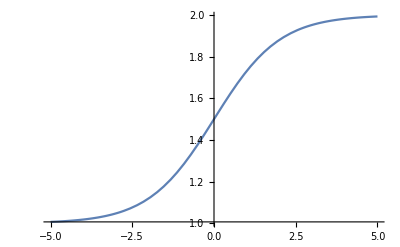

```mathematica
Plot[LogisticSigmoid[x]+1,{x,-5,5}]
```

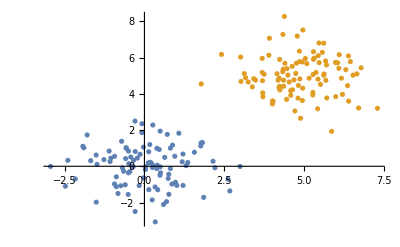

```mathematica
data = {c1 = Table[RandomVariate[MultinormalDistribution[{0,0},{{1,0},{0,1}}]],100],c2 = Table[RandomVariate[MultinormalDistribution[{5,5},{{1,0},{0,1}}]],100]};
ListPlot[data]
```

```mathematica
linearModel = NetChain[{LinearLayer[{}],ElementwiseLayer[(LogisticSigmoid[#] +1)&]},"Input"->2]
```

NetChain[<>]

```mathematica
dataTrain = Join[Map[Rule[#,1]&,c1], Map[Rule[#,2]&,c2]];
```

```mathematica
trainedModelLinear =NetTrain[linearModel,dataTrain]
```

NetChain[<>]

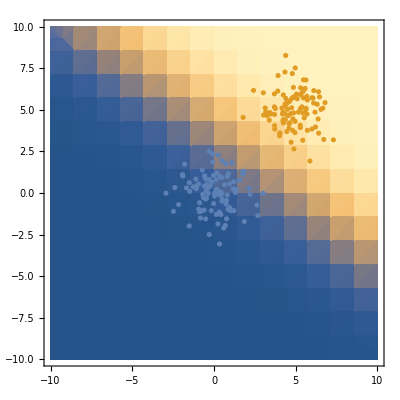

```mathematica
Show[DensityPlot[trainedModelLinear[{x,y}],{x,-10,10},{y,-10,10}],ListPlot[data]]
```

## non linearly separable dataset

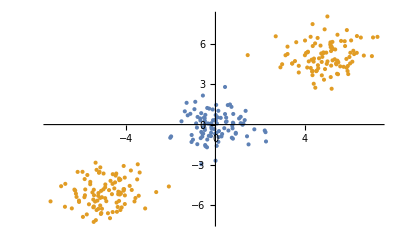

```mathematica
data2 = {c1 = Table[RandomVariate[MultinormalDistribution[{0,0},{{1,0},{0,1}}]],100],c2 = Join[Table[RandomVariate[MultinormalDistribution[{5,5},{{1,0},{0,1}}]],100],
Table[RandomVariate[MultinormalDistribution[{-5,-5},{{1,0},{0,1}}]],100]

]};
ListPlot[data2]
```

```mathematica
dataTrain2 = Join[Map[Rule[#,1]&,c1], Map[Rule[#,2]&,c2]];
```

```mathematica
trainedModelLinear2 =NetTrain[linearModel,dataTrain2]
```

NetChain[<>]

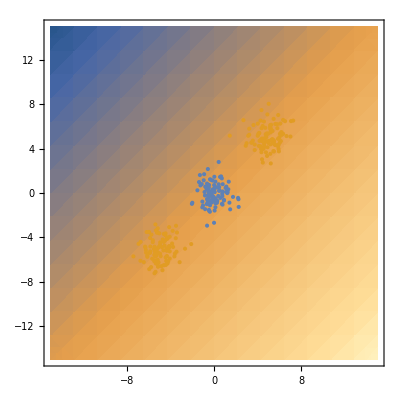

```mathematica
Show[DensityPlot[trainedModelLinear2[{x,y}],{x,-15,15},{y,-15,15}],ListPlot[data2]]
```

## send to higher dimensions

```mathematica
linearModel2 = NetChain[{LinearLayer[2],Ramp,LinearLayer[{}],ElementwiseLayer[(LogisticSigmoid[#] +1)&]},"Input"->2]
```

NetChain[<>]

```mathematica
trainedModelLinear2 =NetTrain[linearModel2,dataTrain2]
```

NetChain[<>]

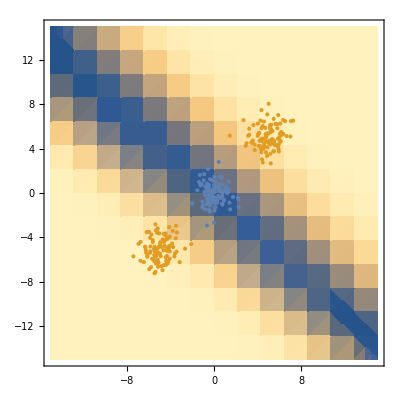

```mathematica
Show[DensityPlot[trainedModelLinear2[{x,y}],{x,-15,15},{y,-15,15}],ListPlot[data2]]
```

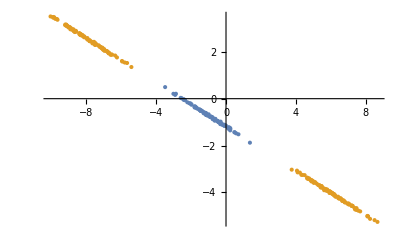

```mathematica
ListPlot[NetExtract[trainedModelLinear2,1] /@ data2]
```

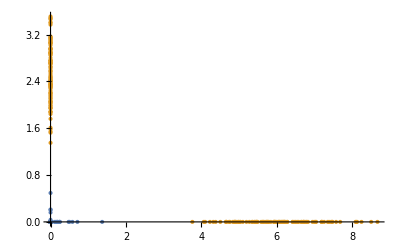

```mathematica
ListPlot[ElementwiseLayer[Ramp][NetExtract[trainedModelLinear2,1] /@ data2]]
```